```mathematica
r=1;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

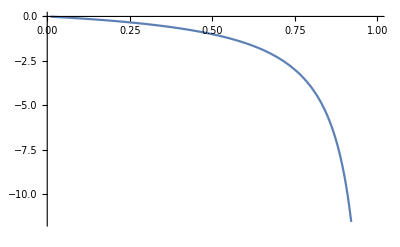
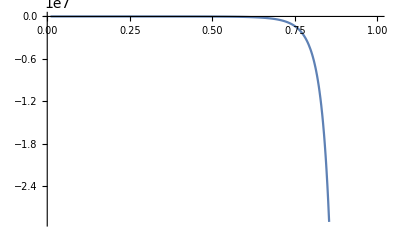
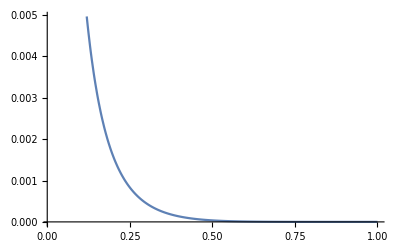
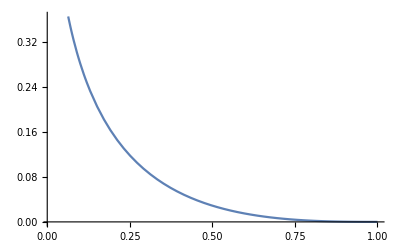
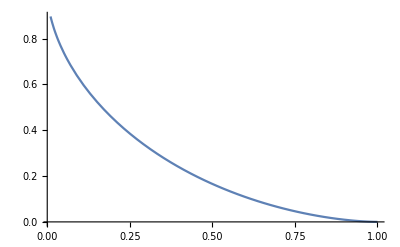
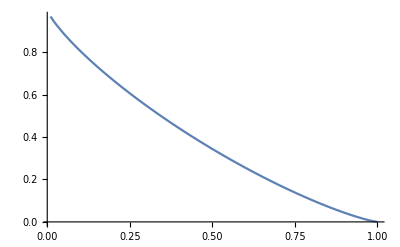
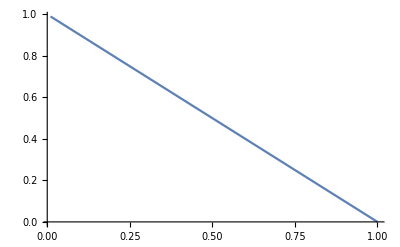
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[(r^i - x^i)^(1/i),{x,0.01,r}],{i,-1, 1, .2}]
```

```mathematica
r=1
areas = Table[Integrate[(r^p - x^p)^(1/p), {x, 0, r}],{p,.6,1.4, .2}]
```

1

```mathematica
Integrate[(d^k - x^k)^(1/k), x]
```

x (d^k-x^k)^(1/k) (1-d^-k x^k)^(-1/k) Hypergeometric2F1[-1/k,1/k,1+1/k,d^-k x^k]

```mathematica
Table[Plot[Integrate[(r^p - x^p)^(1/p), {x, 0, p}],{r, 0.6, 1.4}],{p,.6,1.4, .2}]
```

```mathematica
p=.9;
Plot[Integrate[(r^p - x^p)^(1/p), {x, 0, p}],{r, 0.6, 1.4}]
```

0.9

```mathematica
Clear[r]
i= 0.6;
Table[Integrate[(r^i - x^i)^(1/i),{x,0,r}], {r, 1, }]
```

```mathematica
N[(√π Gamma[4/3])/(2^(2/3) Gamma[5/6])]
```

0.883319

```mathematica
p= .6;
```

```mathematica
r=1.4;
Integrate[(r^p - x^p)^(1/p),{x,0,r}]
```

0.479124